```mathematica
PrependTo[$Path,"/Users/annils14/Documents/KerrModes"];PrependTo[$Path,"~/Research/KerrQNM/KerrModes"];
Needs["KerrTTML`"]
SetSpinWeight[-2]
SelectMode[PolynomialMode]
```

All KerrMode routines (TTML) set for Spin-Weight s = -2

Mode set to find Polynomial solutions

```mathematica
SchTTMLTable[2]=2;
SchTTMLTable[2,0]={-2.00*I,0,0,0,0};
SchTTMLTable[2,1]={-2.00*I,0,0,0,0};
SchTTMLTable[3]=2;
SchTTMLTable[3,0]={-10.0*I,0,0,0,0};
SchTTMLTable[3,1]={-10.0*I,0,0,0,0};
```

```mathematica
SchwarzschildTTML[2,0]
```

Computing (l=2,n=0)

{-2. ⅈ,0,300,-14,0}

```mathematica
Save["/Users/annils14/Documents/KerrModes/KerrTTMLTable_00.dat",KerrTTML]
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_00.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p01.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p02.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p03.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p04.dat";
```

```mathematica
<<"/Users/annils14/Documents/KerrModes/KerrTTMLTable_p05.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_00.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p01.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p02.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p03.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p04.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/KerrTTMLTable_p05.dat";
```

```mathematica
KerrTTML[2,0,{0,0}][[-1]]
```

{8101001/16384000,{-2.59221938844357377362308×10^-27-3.32932464333632508809299 ⅈ,0,300,-8,1.05427856406349503051469×10^-19,300,0,0.654387451804623391671247,24},{5.31169089006987495148787-1.86929049226304246652264×10^-27 ⅈ,12,{0.926314398664427651686731,-2.43605512448961034437431×10^-28-0.362297525389928649821131 ⅈ,-0.101203172569303999014166+1.44835657915437095439063×10^-28 ⅈ,4.52699248059806435096392×10^-29+0.020691886304687763601274 ⅈ,0.00341752527281805138651751-1.01091317404582626241193×10^-29 ⅈ,-1.74497194733624481485521×10^-30-0.000468058577520540482725929 ⅈ,-0.0000551013052586024172915862+2.48084298442211282297944×10^-31 ⅈ,2.98995697994554160239674×10^-32+5.66643235812711576651505×10^-6 ⅈ,5.18537495346009658744474×10^-7-3.13850162493409875158105×10^-33 ⅈ,-2.91415986051870476043666×10^-34-4.26754202753149016890482×10^-8 ⅈ,-3.19443226670194558835269×10^-9+2.42952301019190785071037×10^-35 ⅈ,1.83926163720485453009745×10^-36+2.19370530272997909914795×10^-10 ⅈ}}}

```mathematica
KerrTTML[2,0,{0,2}]=KerrTTML[2,0,{0,1}];
```

```mathematica
KerrModeMakeMultiplet[2,0,0]
```

```mathematica
?ShortenModeSequence
```

ShortenModeSequence[l,m,n,N] removes the first N elements of the Mode sequence (l,m,n)
if N>0, and removes the last N elements if N<0.

Options:
	 ShortenBy→Drop : Drop, Take
		 If 'Take' is chosen, the first N elemets are kept if N>0, and the last N elements
		 are kept if N<0.

```mathematica
1253-563
```

690

```mathematica
Length[KerrTTML[2,0,{0,0}]]
```

573

```mathematica
ShortenModeSequence[2,0,{0,2},-690]
```

Original Length of `1`[`2`,`3`,`4`] = `5`KerrTTML20{0,2}2436

Removing last -690 elements

```mathematica
KerrTTMLSequence[2,0,{0,1},-8,ModeGuess->{0.0004334-3.331*I,4},MaxΔω->10,SeqDirection->Backward]
```

Set $MinPrecision = 24

KerrTTML[2,0,{0,1}] sequence exists with 2238 entries

Increasing Δa, blevel = 4

Untested section of code! 1

Guesses set: 0.0004334-3.331 ⅈ : 4 : 300 : 23

No solution found at a = 0.020875, try decreasing Δa, blevel = 5

ModeSol a=0.02090625 ω=5.71696×10^-38-413.485 ⅈ Alm=14.1172-2.361×10^-39 ⅈ

ModeSol a=0.020875 ω=5.86706×10^-38-414.311 ⅈ Alm=14.1216+2.62811×10^-40 ⅈ

Increasing Δa, blevel = 4

ModeSol a=0.0208125 ω=1.52605×10^-35-415.973 ⅈ Alm=14.1303+3.21798×10^-37 ⅈ

ModeSol a=0.02075 ω=2.48272×10^-34-417.646 ⅈ Alm=14.1391+5.18546×10^-36 ⅈ

Increasing Δa, blevel = 3

ModeSol a=0.020625 ω=6.56943×10^-32-421.028 ⅈ Alm=14.1568+1.36429×10^-33 ⅈ

ModeSol a=0.0205 ω=1.08667×10^-30-424.457 ⅈ Alm=14.1746+2.24265×10^-32 ⅈ

Increasing Δa, blevel = 2

ModeSol a=0.02025 ω=9.92847×10^-31-431.465 ⅈ Alm=14.2106+2.02331×10^-32 ⅈ

No solution found at a = 0.02, try decreasing Δa, blevel = 3

ModeSol+/- a=0.020375 ω=7.9053×10^-32-427.936 ⅈ Alm=14.1925+1.62124×10^-33 ⅈ

ModeSol a=0.020125 ω=1.59806×10^-36-435.045 ⅈ Alm=14.2288+3.13975×10^-38 ⅈ

ModeSol a=0.02 ω=1.69884×10^-35-438.677 ⅈ Alm=14.2472+3.42674×10^-37 ⅈ

Increasing Δa, blevel = 2

Set $MinPrecision =28

ModeSol a=0.01975 ω=2.57627×10^-32-446.101 ⅈ Alm=14.2844+5.11695×10^-34 ⅈ

No solution found at a = 0.0195, try decreasing Δa, blevel = 3

ModeSol+/- a=0.019875 ω=1.06322×10^-31-442.362 ⅈ Alm=14.2657+2.12549×10^-33 ⅈ

ModeSol a=0.019625 ω=5.49678×10^-34-449.896 ⅈ Alm=14.3032+1.08464×10^-35 ⅈ

ModeSol a=0.0195 ω=1.14133×10^-33-453.748 ⅈ Alm=14.3222+2.23711×10^-35 ⅈ

Increasing Δa, blevel = 2

ModeSol a=0.01925 ω=6.17496×10^-31-461.626 ⅈ Alm=14.3606+1.19459×10^-32 ⅈ

No solution found at a = 0.019, try decreasing Δa, blevel = 3

ModeSol+/- a=0.019375 ω=1.44073×10^-31-457.657 ⅈ Alm=14.3413+2.80578×10^-33 ⅈ

ModeSol a=0.019125 ω=6.07981×10^-33-465.655 ⅈ Alm=14.38+1.16835×10^-34 ⅈ

ModeSol a=0.019 ω=9.50474×10^-33-469.745 ⅈ Alm=14.3996+1.81425×10^-34 ⅈ

Increasing Δa, blevel = 2

ModeSol a=0.01875 ω=4.44184×10^-32-478.118 ⅈ Alm=14.4393+8.36417×10^-34 ⅈ

No solution found at a = 0.0185, try decreasing Δa, blevel = 3

ModeSol+/- a=0.018875 ω=1.96774×10^-31-473.899 ⅈ Alm=14.4194+3.73067×10^-33 ⅈ

ModeSol a=0.018625 ω=2.96889×10^-32-482.402 ⅈ Alm=14.4594+5.55236×10^-34 ⅈ

ModeSol a=0.0185 ω=4.12771×10^-32-486.753 ⅈ Alm=14.4797+7.66645×10^-34 ⅈ

Increasing Δa, blevel = 2

Set $MinPrecision =28

ModeSol a=0.01825 ω=3.84043×10^-34-495.665 ⅈ Alm=14.5208+7.03498×10^-36 ⅈ

No solution found at a = 0.018, try decreasing Δa, blevel = 3

ModeSol+/- a=0.018375 ω=2.70993×10^-31-491.174 ⅈ Alm=14.5002+4.99835×10^-33 ⅈ

ModeSol a=0.018125 ω=9.98216×10^-32-500.228 ⅈ Alm=14.5417+1.81552×10^-33 ⅈ

ModeSol a=0.018 ω=1.30262×10^-31-504.866 ⅈ Alm=14.5627+2.35243×10^-33 ⅈ

Increasing Δa, blevel = 2

No solution found at a = 0.01775, try decreasing Δa, blevel = 3

ModeSol a=0.017875 ω=1.68049×10^-31-509.578 ⅈ Alm=14.5839+3.01326×10^-33 ⅈ

ModeSol a=0.01775 ω=2.14591×10^-31-514.368 ⅈ Alm=14.6053+3.82027×10^-33 ⅈ

Increasing Δa, blevel = 2

No solution found at a = 0.0175, try decreasing Δa, blevel = 3

ModeSol a=0.017625 ω=2.71519×10^-31-519.237 ⅈ Alm=14.6268+4.79892×10^-33 ⅈ

ModeSol a=0.0175 ω=3.4072×10^-31-524.187 ⅈ Alm=14.6486+5.97831×10^-33 ⅈ

Increasing Δa, blevel = 2

No solution found at a = 0.01725, try decreasing Δa, blevel = 3

ModeSol a=0.017375 ω=4.24368×10^-31-529.22 ⅈ Alm=14.6706+7.39165×10^-33 ⅈ

Set $MinPrecision =28

ModeSol a=0.01725 ω=7.78445×10^-27-534.338 ⅈ Alm=14.6928+1.34592×10^-28 ⅈ

ModeSol a=0.017125 ω=8.5875×10^-36-539.543 ⅈ Alm=14.7152+1.47517×10^-37 ⅈ

ModeSol a=0.017 ω=1.38294×10^-34-544.837 ⅈ Alm=14.7378+2.35538×10^-36 ⅈ

ModeSol a=0.016875 ω=7.20257×10^-34-550.222 ⅈ Alm=14.7606+1.2177×10^-35 ⅈ

ModeSol a=0.01675 ω=2.35626×10^-33-555.701 ⅈ Alm=14.7836+3.95327×10^-35 ⅈ

ModeSol a=0.016625 ω=5.97141×10^-33-561.276 ⅈ Alm=14.8069+9.94259×10^-35 ⅈ

ModeSol a=0.0165 ω=1.28757×10^-32-566.949 ⅈ Alm=14.8304+2.12737×10^-34 ⅈ

ModeSol a=0.016375 ω=2.48357×10^-32-572.723 ⅈ Alm=14.8541+4.07179×10^-34 ⅈ

ModeSol a=0.01625 ω=4.41591×10^-32-578.601 ⅈ Alm=14.878+7.18342×10^-34 ⅈ

ModeSol a=0.016125 ω=7.37918×10^-32-584.585 ⅈ Alm=14.9022+1.19097×10^-33 ⅈ

ModeSol a=0.016 ω=1.17433×10^-31-590.677 ⅈ Alm=14.9266+1.88033×10^-33 ⅈ

ModeSol a=0.015875 ω=1.79667×10^-31-596.882 ⅈ Alm=14.9513+2.85392×10^-33 ⅈ

Set $MinPrecision =28

ModeSol a=0.01575 ω=2.66122×10^-31-603.201 ⅈ Alm=14.9763+4.19329×10^-33 ⅈ

ModeSol a=0.015625 ω=2.85963×10^-36-609.638 ⅈ Alm=15.0014+4.42265×10^-38 ⅈ

ModeSol a=0.0155 ω=2.03452×10^-34-616.195 ⅈ Alm=15.0269+3.15321×10^-36 ⅈ

ModeSol a=0.015375 ω=1.58236×10^-33-622.877 ⅈ Alm=15.0526+2.4329×10^-35 ⅈ

ModeSol a=0.01525 ω=6.25549×10^-33-629.686 ⅈ Alm=15.0786+9.53799×10^-35 ⅈ

ModeSol a=0.015125 ω=1.77222×10^-32-636.627 ⅈ Alm=15.1048+2.67971×10^-34 ⅈ

ModeSol a=0.015 ω=4.11581×10^-32-643.702 ⅈ Alm=15.1314+6.171×10^-34 ⅈ

ModeSol a=0.014875 ω=8.37621×10^-32-650.916 ⅈ Alm=15.1582+1.24523×10^-33 ⅈ

ModeSol a=0.01475 ω=1.55168×10^-31-658.272 ⅈ Alm=15.1853+2.28705×10^-33 ⅈ

ModeSol a=0.014625 ω=1.704×10^-36-665.775 ⅈ Alm=15.2127+2.31724×10^-38 ⅈ

ModeSol a=0.0145 ω=3.6222×10^-34-673.428 ⅈ Alm=15.2405+5.24814×10^-36 ⅈ

ModeSol a=0.014375 ω=3.43815×10^-33-681.236 ⅈ Alm=15.2685+4.93677×10^-35 ⅈ

Set $MinPrecision =28

ModeSol a=0.01425 ω=1.4802×10^-32-689.204 ⅈ Alm=15.2968+2.10654×10^-34 ⅈ

ModeSol a=0.014125 ω=4.40131×10^-32-697.336 ⅈ Alm=15.3255+6.20791×10^-34 ⅈ

ModeSol a=0.014 ω=1.05524×10^-31-705.637 ⅈ Alm=15.3545+1.475×10^-33 ⅈ

ModeSol a=0.013875 ω=5.03342×10^-36-714.112 ⅈ Alm=15.3839+6.81799×10^-38 ⅈ

ModeSol a=0.01375 ω=8.88415×10^-34-722.767 ⅈ Alm=15.4136+1.21906×10^-35 ⅈ

ModeSol a=0.013625 ω=8.20583×10^-33-731.607 ⅈ Alm=15.4436+1.11582×10^-34 ⅈ

ModeSol a=0.0135 ω=3.49926×10^-32-740.637 ⅈ Alm=15.474+4.71398×10^-34 ⅈ

ModeSol a=0.013375 ω=1.03644×10^-31-749.864 ⅈ Alm=15.5048+1.38312×10^-33 ⅈ

ModeSol a=0.01325 ω=1.27398×10^-34-759.294 ⅈ Alm=15.5359+1.68539×10^-36 ⅈ

No solution found at a = 0.013125, try decreasing Δa, blevel = 4

ModeSol+/- a=0.0133125 ω=3.25394×10^-33-754.554 ⅈ Alm=15.5203+4.32186×10^-35 ⅈ

ModeSol a=0.0131875 ω=5.48042×10^-32-764.087 ⅈ Alm=15.5516+7.20958×10^-34 ⅈ

ModeSol a=0.013125 ω=5.79864×10^-32-768.933 ⅈ Alm=15.5674+7.59157×10^-34 ⅈ

Increasing Δa, blevel = 3

Set $MinPrecision =28

ModeSol a=0.013 ω=3.03569×10^-33-778.788 ⅈ Alm=15.5993+3.93596×10^-35 ⅈ

No solution found at a = 0.012875, try decreasing Δa, blevel = 4

ModeSol+/- a=0.0130625 ω=4.08068×10^-33-773.833 ⅈ Alm=15.5833+5.31669×10^-35 ⅈ

ModeSol a=0.0129375 ω=6.87957×10^-32-783.799 ⅈ Alm=15.6154+8.87633×10^-34 ⅈ

ModeSol a=0.012875 ω=7.2869×10^-32-788.866 ⅈ Alm=15.6317+9.35587×10^-34 ⅈ

ModeSol a=0.0128125 ω=7.72049×10^-32-793.991 ⅈ Alm=15.648+9.86383×10^-34 ⅈ

ModeSol a=0.01275 ω=8.18217×10^-32-799.174 ⅈ Alm=15.6644+1.0402×10^-33 ⅈ

ModeSol a=0.0126875 ω=8.6739×10^-32-804.417 ⅈ Alm=15.6809+1.09724×10^-33 ⅈ

ModeSol a=0.012625 ω=9.1978×10^-32-809.72 ⅈ Alm=15.6975+1.1577×10^-33 ⅈ

ModeSol a=0.0125625 ω=3.54712×10^-28-815.084 ⅈ Alm=15.7143+4.44229×10^-30 ⅈ

ModeSol a=0.0125 ω=1.64016×10^-38-820.511 ⅈ Alm=15.7311-2.81009×10^-39 ⅈ

ModeSol a=0.0124375 ω=3.53733×10^-37-826.002 ⅈ Alm=15.748+2.25298×10^-39 ⅈ

ModeSol a=0.012375 ω=1.82266×10^-36-831.557 ⅈ Alm=15.7651+2.06291×10^-38 ⅈ

Set $MinPrecision =28

ModeSol a=0.0123125 ω=5.88131×10^-36-837.177 ⅈ Alm=15.7823+7.06995×10^-38 ⅈ

ModeSol a=0.01225 ω=1.47063×10^-35-842.865 ⅈ Alm=15.7996+1.79142×10^-37 ⅈ

ModeSol a=0.0121875 ω=3.12618×10^-35-848.62 ⅈ Alm=15.817+3.79184×10^-37 ⅈ

ModeSol a=0.012125 ω=5.9496×10^-35-854.444 ⅈ Alm=15.8345+7.15783×10^-37 ⅈ

ModeSol a=0.0120625 ω=1.0431×10^-34-860.339 ⅈ Alm=15.8521+1.25286×10^-36 ⅈ

ModeSol a=0.012 ω=1.71778×10^-34-866.305 ⅈ Alm=15.8699+2.0556×10^-36 ⅈ

ModeSol a=0.0119375 ω=2.69344×10^-34-872.343 ⅈ Alm=15.8878+3.20385×10^-36 ⅈ

ModeSol a=0.011875 ω=4.05834×10^-34-878.456 ⅈ Alm=15.9058+4.8029×10^-36 ⅈ

ModeSol a=0.0118125 ω=5.91781×10^-34-884.644 ⅈ Alm=15.9239+6.96386×10^-36 ⅈ

ModeSol a=0.01175 ω=8.39504×10^-34-890.909 ⅈ Alm=15.9421+9.82624×10^-36 ⅈ

ModeSol a=0.0116875 ω=1.16343×10^-33-897.251 ⅈ Alm=15.9605+1.35444×10^-35 ⅈ

ModeSol a=0.011625 ω=1.5803×10^-33-903.673 ⅈ Alm=15.979+1.82977×10^-35 ⅈ

Set $MinPrecision =28

ModeSol a=0.0115625 ω=2.11077×10^-33-910.176 ⅈ Alm=15.9976+2.43145×10^-35 ⅈ

ModeSol a=0.0115 ω=2.77296×10^-33-916.761 ⅈ Alm=16.0164+3.17638×10^-35 ⅈ

ModeSol a=0.0114375 ω=3.59629×10^-33-923.43 ⅈ Alm=16.0353+4.09603×10^-35 ⅈ

ModeSol a=0.011375 ω=4.60849×10^-33-930.184 ⅈ Alm=16.0543+5.21998×10^-35 ⅈ

ModeSol a=0.0113125 ω=5.84257×10^-33-937.025 ⅈ Alm=16.0735+6.58117×10^-35 ⅈ

ModeSol a=0.01125 ω=7.33599×10^-33-943.955 ⅈ Alm=16.0928+8.21695×10^-35 ⅈ

ModeSol a=0.0111875 ω=9.13128×10^-33-950.974 ⅈ Alm=16.1123+1.0171×10^-34 ⅈ

ModeSol a=0.011125 ω=1.12765×10^-32-958.085 ⅈ Alm=16.1319+1.24894×10^-34 ⅈ

ModeSol a=0.0110625 ω=1.38258×10^-32-965.29 ⅈ Alm=16.1516+1.52261×10^-34 ⅈ

ModeSol a=0.011 ω=1.68405×10^-32-972.591 ⅈ Alm=16.1715+1.844×10^-34 ⅈ

ModeSol a=0.0109375 ω=2.03894×10^-32-979.988 ⅈ Alm=16.1915+2.21977×10^-34 ⅈ

ModeSol a=0.010875 ω=2.455×10^-32-987.484 ⅈ Alm=16.2117+2.65733×10^-34 ⅈ

Set $MinPrecision =28

ModeSol a=0.0108125 ω=2.94092×10^-32-995.081 ⅈ Alm=16.232+3.16483×10^-34 ⅈ

ModeSol a=0.01075 ω=3.50647×10^-32-1002.78 ⅈ Alm=16.2525+3.75142×10^-34 ⅈ

ModeSol a=0.0106875 ω=5.21237×10^-27-1010.59 ⅈ Alm=16.2731+5.54376×10^-29 ⅈ

ModeSol a=0.010625 ω=2.96014×10^-37-1018.5 ⅈ Alm=16.2939+1.8952×10^-39 ⅈ

ModeSol a=0.0105625 ω=4.75323×10^-36-1026.52 ⅈ Alm=16.3149+4.8245×10^-38 ⅈ

ModeSol a=0.0105 ω=2.43184×10^-35-1034.65 ⅈ Alm=16.336+2.55524×10^-37 ⅈ

ModeSol a=0.0104375 ω=7.74064×10^-35-1042.9 ⅈ Alm=16.3573+5.97051×10^-37 ⅈ

ModeSol a=0.010375 ω=1.96519×10^-34-1051.26 ⅈ Alm=16.3788+1.96157×10^-36 ⅈ

ModeSol a=0.0103125 ω=4.20125×10^-34-1059.74 ⅈ Alm=16.4004+4.31295×10^-36 ⅈ

ModeSol a=0.01025 ω=8.02252×10^-34-1068.33 ⅈ Alm=16.4222+8.18098×10^-36 ⅈ

ModeSol a=0.0101875 ω=1.41236×10^-33-1077.06 ⅈ Alm=16.4441+1.43161×10^-35 ⅈ

ModeSol a=0.010125 ω=2.33678×10^-33-1085.9 ⅈ Alm=16.4663+2.3535×10^-35 ⅈ

Set $MinPrecision =28

ModeSol a=0.0100625 ω=3.69413×10^-33-1094.88 ⅈ Alm=16.4886+3.70679×10^-35 ⅈ

ModeSol a=0.01 ω=5.57644×10^-33-1103.98 ⅈ Alm=16.5111+5.55283×10^-35 ⅈ

ModeSol a=0.0099375 ω=8.17485×10^-33-1113.22 ⅈ Alm=16.5338+8.08572×10^-35 ⅈ

ModeSol a=0.009875 ω=1.16616×10^-32-1122.6 ⅈ Alm=16.5567+1.14579×10^-34 ⅈ

ModeSol a=0.0098125 ω=1.62553×10^-32-1132.11 ⅈ Alm=16.5798+1.58759×10^-34 ⅈ

ModeSol a=0.00975 ω=2.22102×10^-32-1141.77 ⅈ Alm=16.603+2.15322×10^-34 ⅈ

ModeSol a=0.0096875 ω=9.79794×10^-38-1151.57 ⅈ Alm=16.6265+9.49941×10^-39 ⅈ

ModeSol a=0.009625 ω=7.99889×10^-36-1161.52 ⅈ Alm=16.6501+7.58181×10^-38 ⅈ

ModeSol a=0.0095625 ω=5.79315×10^-35-1171.62 ⅈ Alm=16.674+5.48097×10^-37 ⅈ

ModeSol+ a=0.00965625 ω=4.15186×10^-35-1156.53 ⅈ Alm=16.6383+3.96724×10^-37 ⅈ

ModeSol- a=0.00959375 ω=4.12609×10^-35-1166.55 ⅈ Alm=16.662+3.92458×10^-37 ⅈ

Decreasing Δa, blevel = 5

ModeSol a=0.00953125 ω=6.84151×10^-34-1176.73 ⅈ Alm=16.686+6.48048×10^-36 ⅈ

ModeSol a=0.0095 ω=7.11445×10^-34-1181.88 ⅈ Alm=16.6981+6.72105×10^-36 ⅈ

ModeSol a=0.00946875 ω=7.39938×10^-34-1187.06 ⅈ Alm=16.7102+6.96614×10^-36 ⅈ

Set $MinPrecision =28

ModeSol a=0.0094375 ω=7.69655×10^-34-1192.29 ⅈ Alm=16.7223+7.21886×10^-36 ⅈ

ModeSol a=0.00940625 ω=8.00693×10^-34-1197.56 ⅈ Alm=16.7345+7.48704×10^-36 ⅈ

ModeSol a=0.009375 ω=8.33078×10^-34-1202.87 ⅈ Alm=16.7468+7.76306×10^-36 ⅈ

ModeSol a=0.00934375 ω=8.66876×10^-34-1208.22 ⅈ Alm=16.7591+8.05036×10^-36 ⅈ

ModeSol a=0.0093125 ω=9.02191×10^-34-1213.61 ⅈ Alm=16.7715+8.35264×10^-36 ⅈ

ModeSol a=0.00928125 ω=9.39044×10^-34-1219.04 ⅈ Alm=16.7839+8.66278×10^-36 ⅈ

ModeSol a=0.00925 ω=9.76966×10^-34-1224.52 ⅈ Alm=16.7964+8.88737×10^-36 ⅈ

ModeSol a=0.00921875 ω=1.01777×10^-33-1230.04 ⅈ Alm=16.809+9.32628×10^-36 ⅈ

ModeSol a=0.0091875 ω=1.05977×10^-33-1235.6 ⅈ Alm=16.8216+9.67845×10^-36 ⅈ

ModeSol a=0.00915625 ω=1.10368×10^-33-1241.21 ⅈ Alm=16.8342+1.00454×10^-35 ⅈ

ModeSol a=0.009125 ω=1.14955×10^-33-1246.86 ⅈ Alm=16.8469+1.04273×10^-35 ⅈ

ModeSol a=0.00909375 ω=1.1975×10^-33-1252.56 ⅈ Alm=16.8597+1.08213×10^-35 ⅈ

Set $MinPrecision =28

ModeSol a=0.0090625 ω=1.24762×10^-33-1258.3 ⅈ Alm=16.8725+1.12355×10^-35 ⅈ

ModeSol a=0.00903125 ω=1.30003×10^-33-1264.09 ⅈ Alm=16.8854+1.16718×10^-35 ⅈ

ModeSol a=0.009 ω=1.35484×10^-33-1269.92 ⅈ Alm=16.8983+1.21208×10^-35 ⅈ

ModeSol a=0.00896875 ω=1.41213×10^-33-1275.81 ⅈ Alm=16.9113+1.25854×10^-35 ⅈ

ModeSol a=0.0089375 ω=1.47209×10^-33-1281.74 ⅈ Alm=16.9244+1.30757×10^-35 ⅈ

ModeSol a=0.00890625 ω=1.53479×10^-33-1287.72 ⅈ Alm=16.9375+1.35824×10^-35 ⅈ

ModeSol a=0.008875 ω=1.60041×10^-33-1293.75 ⅈ Alm=16.9507+1.41149×10^-35 ⅈ

ModeSol a=0.00884375 ω=1.66907×10^-33-1299.82 ⅈ Alm=16.9639+1.46691×10^-35 ⅈ

ModeSol a=0.0088125 ω=1.74094×10^-33-1305.95 ⅈ Alm=16.9772+1.52445×10^-35 ⅈ

ModeSol a=0.00878125 ω=1.81617×10^-33-1312.13 ⅈ Alm=16.9906+1.58484×10^-35 ⅈ

ModeSol a=0.00875 ω=1.89495×10^-33-1318.36 ⅈ Alm=17.004+1.64754×10^-35 ⅈ

ModeSol a=0.00871875 ω=1.97742×10^-33-1324.64 ⅈ Alm=17.0175+1.71317×10^-35 ⅈ

Set $MinPrecision =28

ModeSol a=0.0086875 ω=2.04719×10^-33-1330.98 ⅈ Alm=17.0311+1.76711×10^-35 ⅈ

ModeSol a=0.00865625 ω=2.15429×10^-33-1337.37 ⅈ Alm=17.0447+1.85298×10^-35 ⅈ

ModeSol a=0.008625 ω=2.24906×10^-33-1343.81 ⅈ Alm=17.0584+1.92757×10^-35 ⅈ

ModeSol a=0.00859375 ω=2.3484×10^-33-1350.3 ⅈ Alm=17.0721+2.00503×10^-35 ⅈ

ModeSol a=0.0085625 ω=2.45252×10^-33-1356.86 ⅈ Alm=17.0859+2.08658×10^-35 ⅈ

ModeSol a=0.00853125 ω=2.56165×10^-33-1363.46 ⅈ Alm=17.0998+2.17113×10^-35 ⅈ

ModeSol a=0.0085 ω=2.67607×10^-33-1370.13 ⅈ Alm=17.1137+2.25989×10^-35 ⅈ

ModeSol a=0.00846875 ω=2.79601×10^-33-1376.85 ⅈ Alm=17.1277+2.35242×10^-35 ⅈ

ModeSol a=0.0084375 ω=2.92181×10^-33-1383.63 ⅈ Alm=17.1418+2.44925×10^-35 ⅈ

ModeSol a=0.00840625 ω=3.05376×10^-33-1390.47 ⅈ Alm=17.156+2.55023×10^-35 ⅈ

ModeSol a=0.008375 ω=3.19221×10^-33-1397.36 ⅈ Alm=17.1702+2.65607×10^-35 ⅈ

ModeSol a=0.00834375 ω=3.33748×10^-33-1404.32 ⅈ Alm=17.1845+2.76659×10^-35 ⅈ

Set $MinPrecision =28

ModeSol a=0.0083125 ω=3.48991×10^-33-1411.34 ⅈ Alm=17.1988+2.8819×10^-35 ⅈ

ModeSol a=0.00828125 ω=3.64994×10^-33-1418.42 ⅈ Alm=17.2133+3.00273×10^-35 ⅈ

ModeSol a=0.00825 ω=3.81794×10^-33-1425.56 ⅈ Alm=17.2278+3.12879×10^-35 ⅈ

ModeSol a=0.00821875 ω=3.99435×10^-33-1432.76 ⅈ Alm=17.2423+3.26093×10^-35 ⅈ

ModeSol a=0.0081875 ω=4.17964×10^-33-1440.03 ⅈ Alm=17.257+3.39926×10^-35 ⅈ

ModeSol a=0.00815625 ω=4.37425×10^-33-1447.37 ⅈ Alm=17.2717+3.54396×10^-35 ⅈ

ModeSol a=0.008125 ω=4.57876×10^-33-1454.77 ⅈ Alm=17.2865+3.69514×10^-35 ⅈ

ModeSol a=0.00809375 ω=4.79362×10^-33-1462.23 ⅈ Alm=17.3014+3.85374×10^-35 ⅈ

ModeSol a=0.0080625 ω=5.01945×10^-33-1469.77 ⅈ Alm=17.3163+4.01995×10^-35 ⅈ

ModeSol a=0.00803125 ω=5.25686×10^-33-1477.37 ⅈ Alm=17.3313+4.19331×10^-35 ⅈ

ModeSol a=0.008 ω=5.50648×10^-33-1485.04 ⅈ Alm=17.3464+4.37558×10^-35 ⅈ

ModeSol a=0.00796875 ω=5.76902×10^-33-1492.78 ⅈ Alm=17.3616+4.56559×10^-35 ⅈ

Set $MinPrecision =28

ModeSol a=0.0079375 ω=6.0454×10^-33-1500.59 ⅈ Alm=17.3769+4.76626×10^-35 ⅈ

ModeSol a=0.00790625 ω=6.33602×10^-33-1508.48 ⅈ Alm=17.3922+4.98076×10^-35 ⅈ

ModeSol a=0.007875 ω=6.64177×10^-33-1516.43 ⅈ Alm=17.4076+5.2013×10^-35 ⅈ

ModeSol a=0.00784375 ω=6.96364×10^-33-1524.46 ⅈ Alm=17.4231+5.43341×10^-35 ⅈ

ModeSol a=0.0078125 ω=7.30252×10^-33-1532.57 ⅈ Alm=17.4387+5.67755×10^-35 ⅈ

ModeSol a=0.00778125 ω=7.65833×10^-33-1540.75 ⅈ Alm=17.4543+5.91823×10^-35 ⅈ

ModeSol a=0.00775 ω=-6.81937×10^-39-1549.01 ⅈ Alm=17.4701+8.97484×10^-40 ⅈ

ModeSol a=0.00771875 ω=-5.02582×10^-40-1557.34 ⅈ Alm=17.4859-9.85347×10^-40 ⅈ

ModeSol a=0.0076875 ω=5.30426×10^-38-1565.76 ⅈ Alm=17.5018-1.67824×10^-39 ⅈ

ModeSol a=0.00765625 ω=1.64685×10^-37-1574.25 ⅈ Alm=17.5178+3.15209×10^-39 ⅈ

ModeSol a=0.007625 ω=4.55527×10^-37-1582.83 ⅈ Alm=17.5339+3.53218×10^-39 ⅈ

ModeSol a=0.00759375 ω=9.65285×10^-37-1591.48 ⅈ Alm=17.55+8.37138×10^-39 ⅈ

Set $MinPrecision =28

ModeSol a=0.0075625 ω=1.84107×10^-36-1600.23 ⅈ Alm=17.5663+1.26566×10^-38 ⅈ

ModeSol a=0.00753125 ω=5.42507×10^-36-1609.05 ⅈ Alm=17.5826+3.50428×10^-37 ⅈ

ModeSol a=0.0075 ω=7.43238×10^-36-1617.96 ⅈ Alm=17.5991+3.48358×10^-37 ⅈ

ModeSol a=0.00746875 ω=1.02744×10^-35-1626.96 ⅈ Alm=17.6156+3.4997×10^-37 ⅈ

ModeSol a=0.0074375 ω=7.74961×10^-36-1636.04 ⅈ Alm=17.6322-6.1332×10^-37 ⅈ

ModeSol a=0.00740625 ω=1.95275×10^-35-1645.22 ⅈ Alm=17.6489+3.33711×10^-37 ⅈ

ModeSol a=0.007375 ω=2.58799×10^-35-1654.48 ⅈ Alm=17.6657+2.15826×10^-37 ⅈ

ModeSol a=0.00734375 ω=3.55043×10^-35-1663.84 ⅈ Alm=17.6826+2.70688×10^-37 ⅈ

ModeSol a=0.0073125 ω=5.0651×10^-35-1673.29 ⅈ Alm=17.6996+7.56463×10^-37 ⅈ

$Aborted

```mathematica
ShortenModeSequence[2,0,{0,1},-100]
```

Original Length of `1`[`2`,`3`,`4`] = `5`KerrTTML20{0,1}66

Removing last -100 elements

Drop::drop: Cannot drop positions -100 through -1 in {«1»}.

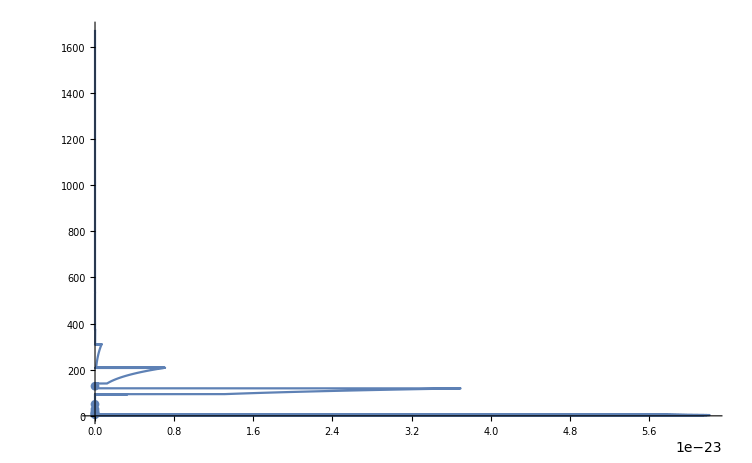

```mathematica
ModePlotOmega[2,0,{0,2}]
```

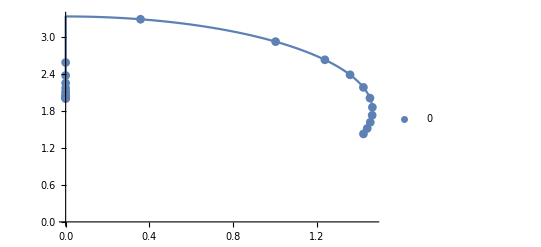

```mathematica
ModePlotOmega[2,0,PlotLegends->Automatic]
```

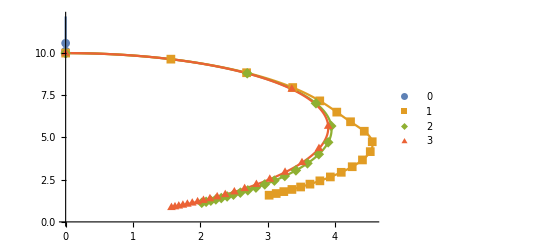

```mathematica
ModePlotOmega[3,0,PlotLegends->Automatic]
```

```mathematica
Head[Re]
```

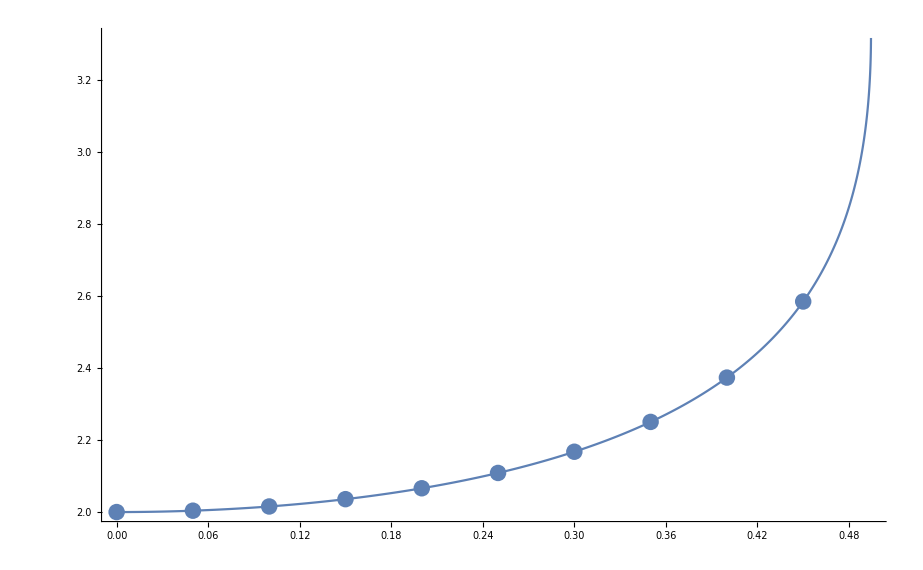

```mathematica
Show[ListLinePlot[KerraOmegaList[2,0,0,Im],PlotRange->All],ListPlot[KerraOmegaListS[2,0,0,Im],PlotRange->All]]
```

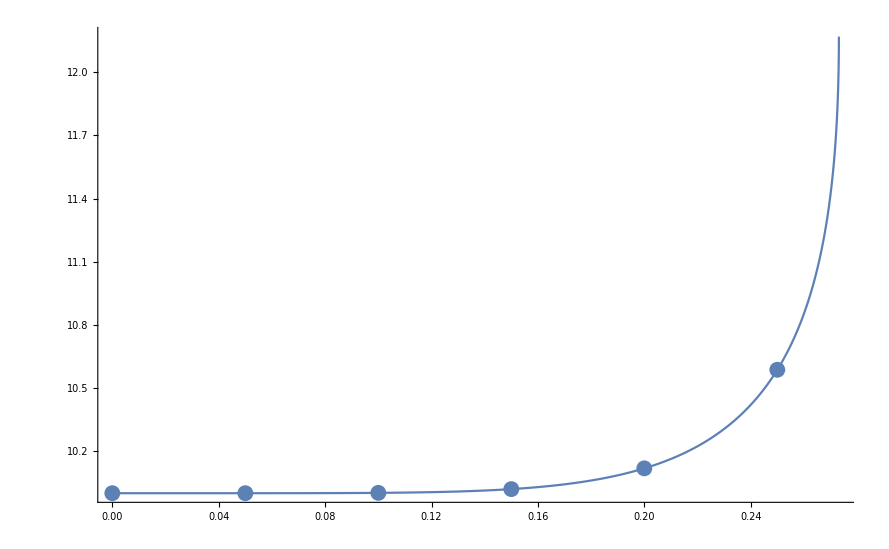

```mathematica
Show[ListLinePlot[KerraOmegaList[3,0,0,Im],PlotRange->All],ListPlot[KerraOmegaListS[3,0,0,Im],PlotRange->All]]
```

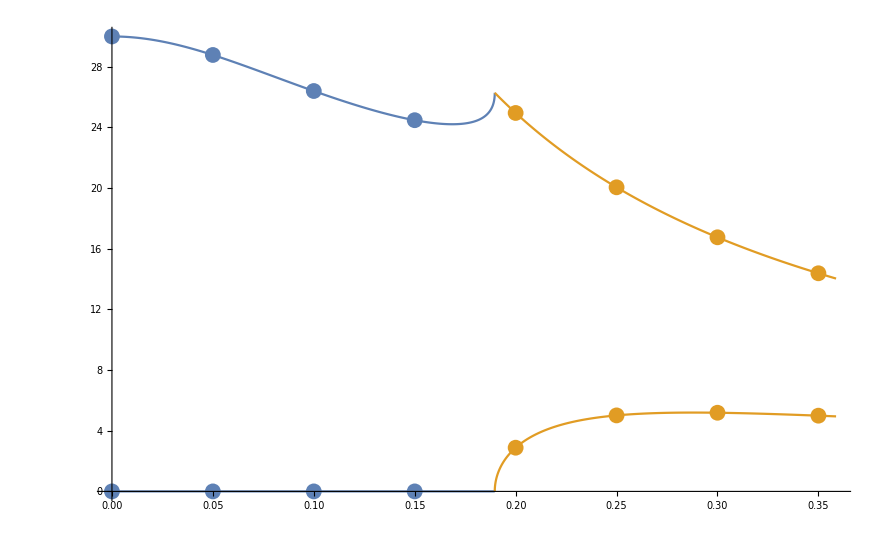

```mathematica
Show[ListLinePlot[{KerraOmegaList[4,0,{0,0},Re],KerraOmegaList[4,0,{0,1},Re]},PlotRange->All],ListLinePlot[{KerraOmegaList[4,0,{0,0},Im],KerraOmegaList[4,0,{0,1},Im]},PlotRange->All],ListPlot[{KerraOmegaListS[4,0,{0,0},Re],KerraOmegaListS[4,0,{0,1},Re]},PlotRange->All],ListPlot[{KerraOmegaListS[4,0,{0,0},Im],KerraOmegaListS[4,0,{0,1},Im]},PlotRange->All],PlotRange->All]
```

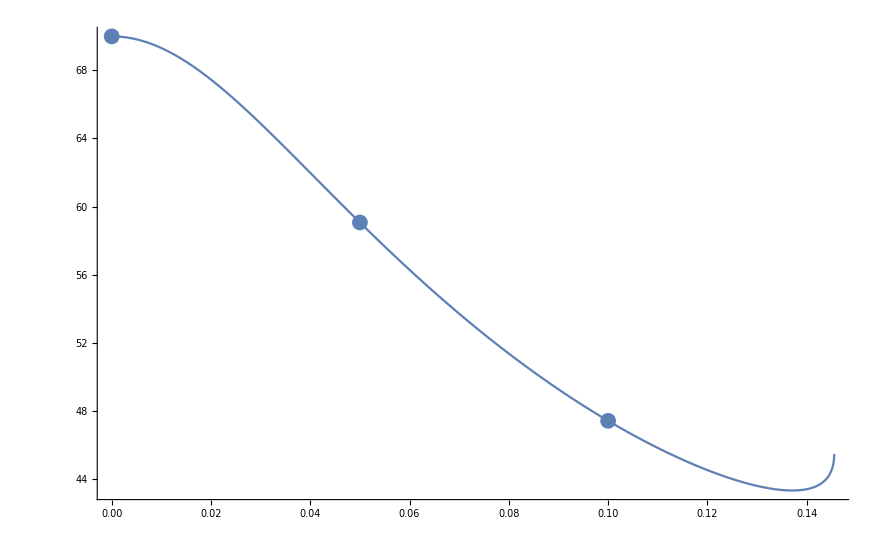

```mathematica
Show[ListLinePlot[KerraOmegaList[5,0,0,Im],PlotRange->All],ListPlot[KerraOmegaListS[5,0,0,Im],PlotRange->All]]
```

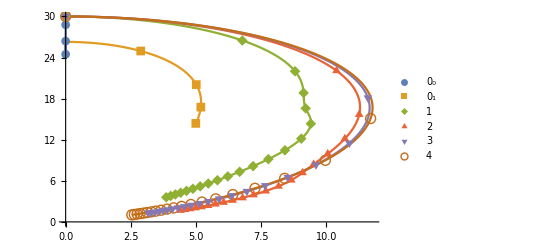

```mathematica
ModePlotOmega[4,0,OTmultiple->{{0,2}},PlotLegends->Automatic]
```

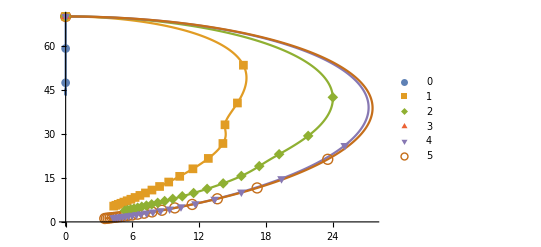

```mathematica
ModePlotOmega[5,0,PlotLegends->Automatic]
```

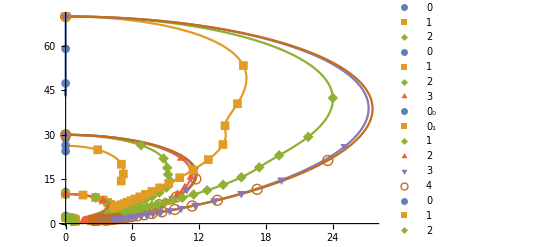

```mathematica
Show[ModePlotOmega[2,0,PlotLegends->Automatic],ModePlotOmega[3,0,PlotLegends->Automatic],ModePlotOmega[4,0,OTmultiple->{{0,2}},PlotLegends->Automatic],ModePlotOmega[5,0,PlotLegends->Automatic],PlotRange->All]
```

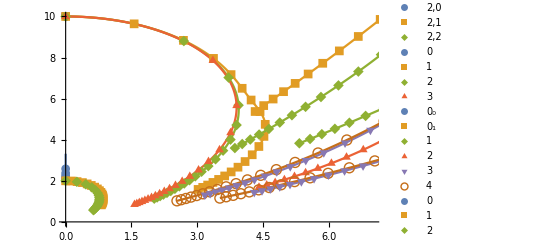

```mathematica
Show[ModePlotOmega[2,0,PlotLegends->{"2,0","2,1","2,2"}],ModePlotOmega[3,0,PlotLegends->Automatic],ModePlotOmega[4,0,OTmultiple->{{0,2}},PlotLegends->Automatic],ModePlotOmega[5,0,PlotLegends->Automatic],PlotRange->{{0,7},{0,10}}]
```

```mathematica
N[KerrTTML[5,0,0][[-1,1]]]
```

0.145536

```mathematica
SchwarzschildTTML[2,0]
```

Computing (l=2,n=0)

{-2. ⅈ,0,300,-14,0}

```mathematica
KerrTTML[2,2,0]
```

{{0,{-2. ⅈ,0,300,-8,0,300,0,331776.000000000000000207,24},{4,4,{1,0,0,0}}},{1/2000,{0.0026666551652701076511193-1.99999487833507862105213 ⅈ,0,300,-8,0,300,0,331776.51960208453111348,24},{3.99999717990467919850917+0.00266666174017775079459347 ⅈ,5,{0.999999982363372167617326,2.45198052526124432820479×10^-7-0.000187811592969986840825002 ⅈ,-2.78872753541199755742722×10^-8-7.48167775047200787673528×10^-11 ⅈ,-1.29606779995223449195122×10^-14+3.21043318440435795820121×10^-12 ⅈ,3.04926317239405376162335×10^-16+1.64480446339400126503193×10^-18 ⅈ}}},{3/2000,{0.00799968947809541011313172-1.99995390704600226284234 ⅈ,0,300,-8,0,300,0,331780.676075117104566321,24},{3.99997461989802179727934+0.00799986699017724450226571 ⅈ,5,{0.999999841274415211014372,2.20670893774846144035319×10^-6-0.000563423652173946337065283 ⅈ,-2.50971528877109553218675×10^-7-2.01994211610712568678682×10^-9 ⅈ,-1.04973026766727508503315×10^-12+8.66725489042023327544275×10^-11 ⅈ,2.46948254168269799281964×10^-14+3.99642989655920669598578×10^-16 ⅈ}}}}

```mathematica
SchwarzschildTTML[3,0]
```

Computing (l=3,n=0)

{-10. ⅈ,0,300,-14,0}

```mathematica
KerrTTMLSequence[2,2,0,-8,SeqDirection->Forward]
```

Set $MinPrecision = 24

KerrTTML[2,2,0] sequence exists with 2 entries

Untested section of code! 2

ModeSol a=0.0015 ω=0.00799969-1.99995 ⅈ Alm=3.99997+0.00799987 ⅈ

KerrModes`Private`AdaptCheck3::incorrectam: Incorrect Δa(-)

$Aborted

```mathematica
KerrTTMLSequence[2,2,0,-8,SeqDirection->Forward,ModeGuess->{0.005348-2*I,4}]
```

Set $MinPrecision = 24

KerrTTML[2,2,0] sequence exists with 3 entries

Untested section of code! 1

Guesses set: 0.005348-2. ⅈ : 4 : 300 : 5

Part::partd: Part specification {«1»}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {«1»}⟦0,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

KerrModes`Private`KerrModeSequence::invalidcall: Invalid call to ModeSolution

$Aborted

```mathematica
Clear[KerrTTML]
```

```mathematica
N[KerrTTML[2,0,{0,0}][[-1,1]]]
```

0.493375

```mathematica
KerrModeMakeMultiplet[2,0,0]
```

```mathematica
Show[ModePlotOmega[2,0,{0,0}],ModePlotOmega[2,0,{0,1}],PlotRange->All]
```

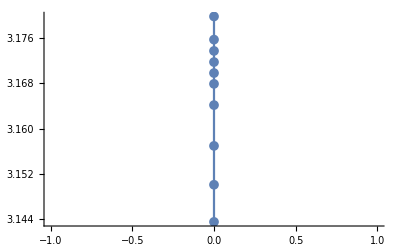

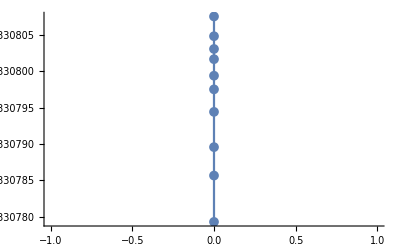

```mathematica
ListLinePlot[Chop[Take[KerrOmegaList[2,0,{0,0}],-10]],PlotRange->Automatic,PlotMarkers->{Automatic, 10}]
```

```mathematica
ShortenModeSequence[2,0,{0,1},1]
```

Original Length of KerrQNM[2,0,{0,1}]=117

Removing first 1 elements

```mathematica
<<"~/Research/KerrQNM/KerrModes/TTMLmodes.dat";
```

```mathematica
<<"~/Research/KerrQNM/KerrModes/QNMmodes.dat";
```

```mathematica
2.0299287138129135*^-39-3.1841050359735195 ⅈ
```

```mathematica
5.20388156758105+2.0875615531508266*^-39 ⅈ
```

```mathematica
Options[KerrTTMLSequence]
```

{CurvatureRatio→1/2,ExtrapolationOrder→2,JacobianStep→-10,Maxblevel→20,Maximalaϵ→10,MaxΔω→0.01,Minblevel→0,ModeaStart→0,ModeGuess→0,ModePrecision→24,NoNegω→False,RadialCFDepth→1,RadialCFDigits→8,RadialCFMinDepth→300,RadialDebug→0,RadialRelax→1,Rootϵ→Null[],SeqDirection→Forward,SolutionDebug→0,SolutionIter→50,SolutionOscillate→10,SolutionRelax→1,SolutionSlow→10,SolutionWindowl→1/2,SolutionWindowt→1/3,SpinWeight→-2}

```mathematica
KerrTTMLSequence[2,0,{0,0},-8,Minblevel->26,Maxblevel->30,SolutionDebug->0,RadialDebug->0]
```

Set $MinPrecision = 24

KerrTTML[2,0,{0,0}] sequence exists with 596 entries

ModeSol a=0.4944459549188613892 ω=0.0000101558-3.33081 ⅈ Alm=5.31276+7.32555×10^-6 ⅈ

ModeSol+ a=0.4944459548890590668 ω=4.79096×10^-24-3.33079 ⅈ Alm=5.31275+3.45578×10^-24 ⅈ

ModeSol+ a=0.494445954903960228 ω=-2.00732×10^-23-3.33079 ⅈ Alm=5.31275-1.44791×10^-23 ⅈ

ModeSol+ a=0.4944459549114108086 ω=1.43549×10^-21-3.3308 ⅈ Alm=5.31276+1.03544×10^-21 ⅈ

ModeSol+ a=0.4944459549151360989 ω=3.8389×10^-6-3.33081 ⅈ Alm=5.31276+2.76906×10^-6 ⅈ

ModeSol+ a=0.494445954916998744 ω=7.67716×10^-6-3.33081 ⅈ Alm=5.31276+5.53766×10^-6 ⅈ

ModeSol- a=0.4944459549132734537 ω=6.81813×10^-19-3.3308 ⅈ Alm=5.31276+4.91802×10^-19 ⅈ

ModeSol+ a=0.4944459549142047763 ω=4.96472×10^-21-3.33081 ⅈ Alm=5.31276+3.58113×10^-21 ⅈ

ModeSol- a=0.4944459549123421311 ω=-8.75194×10^-22-3.3308 ⅈ Alm=5.31276-6.31291×10^-22 ⅈ

ModeSol- a=0.4944459549076855183 ω=-1.29786×10^-21-3.3308 ⅈ Alm=5.31275-9.36163×10^-22 ⅈ

ModeSol-- a=0.4944459549095481634 ω=1.58218×10^-29-3.3308 ⅈ Alm=5.31275+1.14125×10^-29 ⅈ

ModeSol- a=0.4944459548965096474 ω=-3.50654×10^-22-3.33079 ⅈ Alm=5.31275-2.52932×10^-22 ⅈ

ModeSol- a=0.4944459548741579056 ω=-5.32138×10^-25-3.33078 ⅈ Alm=5.31274-3.83837×10^-25 ⅈ

ModeSol- a=0.494445954829454422 ω=2.64273×10^-23-3.33077 ⅈ Alm=5.31273+1.90623×10^-23 ⅈ

ModeSol+ a=0.4944459548443555832 ω=1.92852×10^-23-3.33077 ⅈ Alm=5.31273+1.39106×10^-23 ⅈ

ModeSol- a=0.4944459548145532608 ω=3.80976×10^-24-3.33076 ⅈ Alm=5.31273+2.74802×10^-24 ⅈ

Decreasing Δa, blevel = 29

ModeSol a=0.4944459549207240343 ω=0.0000121385-3.33081 ⅈ Alm=5.31276+8.75566×10^-6 ⅈ

ModeSol a=0.4944459549225866795 ω=0.0000138399-3.33081 ⅈ Alm=5.31276+9.98297×10^-6 ⅈ

Increasing Δa, blevel = 28

ModeSol a=0.4944459549263119698 ω=0.0000167316-3.33081 ⅈ Alm=5.31276+0.0000120688 ⅈ

Increasing Δa, blevel = 27

ModeSol a=0.4944459549337625504 ω=0.0000213718-3.33081 ⅈ Alm=5.31276+0.0000154158 ⅈ

Increasing Δa, blevel = 26

ModeSol a=0.4944459549486637115 ω=0.0000284669-3.33081 ⅈ Alm=5.31276+0.0000205337 ⅈ

ModeSol a=0.4944459549635648727 ω=0.0000341171-3.33081 ⅈ Alm=5.31276+0.0000246092 ⅈ

$Aborted

```mathematica
N[KerrTTML[2,0,{0,0}][[{-2,-1},1]],20]
```

{0.49444595491327345371,0.49444595491420477629}

```mathematica
ShortenModeSequence[2,0,{0,0},-9]
```

Original Length of `1`[`2`,`3`,`4`] = `5`KerrModes`Private`SpinWeightTable20{0,0}618

Removing last -9 elements

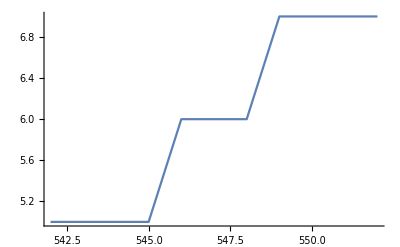

Set $MinPrecision = 24

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->FixAdapt,Maxblevel->7,RefinementPlot->SeqLevel,Refinement->{-12,-1},Index->True]
```

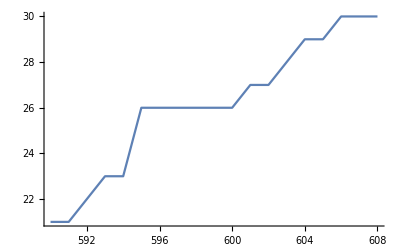

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->None,Maxblevel->4,RefinementPlot->SeqLevel,Refinement->{-20,-1},Index->True]
```

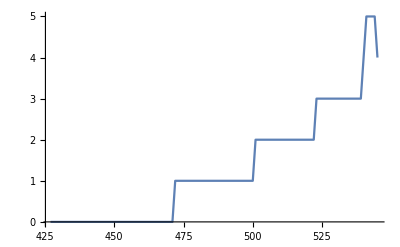

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->RemoveLevels,Maxblevel->4,RefinementPlot->SeqLevel,Refinement->{-120,-1},Index->True]
```

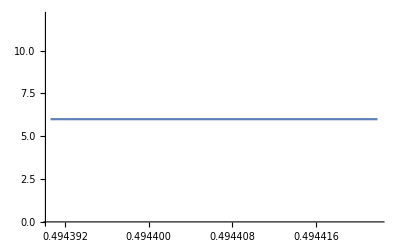

Set $MinPrecision = 24

debug : s = -2 l = 2 m = 0 ϵ = -8 relax = 1 index0 = 567 blevel = 6 forward = False incflag = False

ModeSol+ a=0.4944296875 ω=2.03323×10^-28-3.3113 ⅈ Alm=5.29863+1.46115×10^-28 ⅈ

ModeSol- a=0.4944140625 ω=3.68686×10^-31-3.30356 ⅈ Alm=5.29301+2.64549×10^-31 ⅈ

debug : s = -2 l = 2 m = 0 ϵ = -8 relax = 1 index0 = 566 blevel = 6 forward = False incflag = True

ModeSol- a=0.4943984375 ω=1.33542×10^-23-3.29762 ⅈ Alm=5.28867+9.57087×10^-24 ⅈ

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->RefineAdapt,Minblevel->7,RefinementPlot->SeqLevel,Refinement->{-4,-1},SolutionDebug->0,RadialDebug->0]
```

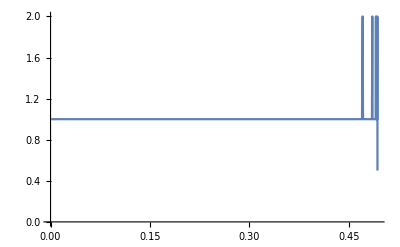

```mathematica
KerrTTMLRefineSequence[2,0,{0,0},-8,RefinementAction->None,RefinementPlot->StepRatio]
```

```mathematica
t=Null[]
```

Null[]

```mathematica
MemberQ[{QNM,TTML,TTMR},QNM]
```

True

```mathematica
QNM!=Null[]
```

QNM≠Null[]

Part::partd: Part specification KerrQNM[2,0,{8,0}]⟦1,2,1⟧ is longer than depth of object.

Part::partd: Part specification KerrQNM[2,0,{8,0}]⟦2,2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

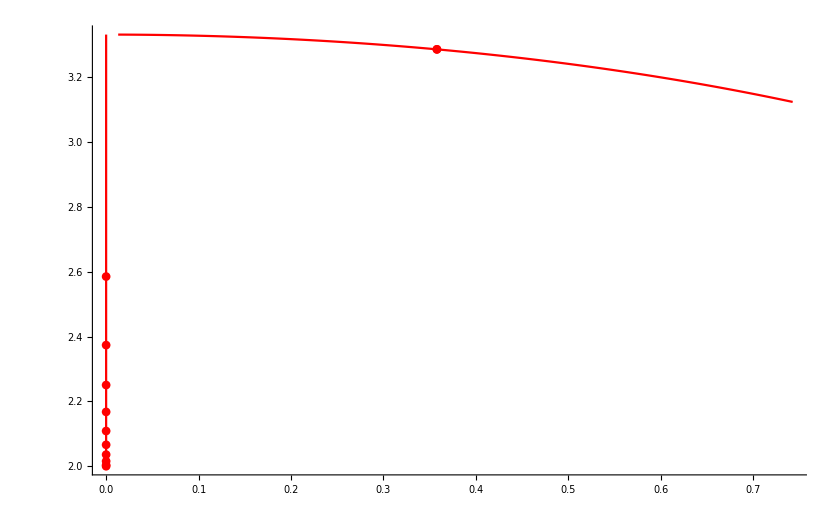

```mathematica
Show[ModePlotOmega[2,0,{0,0},PlotStyle->Red],ModePlotOmega[2,0,{0,1},PlotStyle->Red],ModePlotOmega[2,0,{8,0},ModeType->QNM],PlotRange->All]
```

```mathematica
?ShortenModeSequence
```

ShortenModeSequence[l,m,n,N] removes the first N elements of the Mode sequence (l,m,n)
if N>0, and removes the last N elements if N<0.

Options:
	 ShortenBy→Drop : Drop, Take
		 If 'Take' is chosen, the first N elemets are kept if N>0, and the last N elements
		 are kept if N<0.

```mathematica
KerrTTMLSequence[2,0,{0,1},-8,SeqDirection->Backward,ModeaStart->{51/100,0.578-3.21ⅈ,4}]
```

$Aborted

```mathematica
ShortenModeSequence[2,1,0,-5,ShortenBy->Take]
```

Original Length of KerrQNM[2,1,0]=30

Taking last -5 elements

```mathematica
N[KerrTTML[2,1,0][[1,1]]]
```

0.03

```mathematica
KerrTTML[2,0,{0,0}][[-1]]
```

{8101001/16384000,{-2.59221938844357377362308×10^-27-3.32932464333632508809299 ⅈ,0,300,-8,1.05427856406349503051469×10^-19,300,0,0.654387451804623391671247,24},{5.31169089006987495148787-1.86929049226304246652264×10^-27 ⅈ,12,{0.926314398664427651686731,-2.43605512448961034437431×10^-28-0.362297525389928649821131 ⅈ,-0.101203172569303999014166+1.44835657915437095439063×10^-28 ⅈ,4.52699248059806435096392×10^-29+0.020691886304687763601274 ⅈ,0.00341752527281805138651751-1.01091317404582626241193×10^-29 ⅈ,-1.74497194733624481485521×10^-30-0.000468058577520540482725929 ⅈ,-0.0000551013052586024172915862+2.48084298442211282297944×10^-31 ⅈ,2.98995697994554160239674×10^-32+5.66643235812711576651505×10^-6 ⅈ,5.18537495346009658744474×10^-7-3.13850162493409875158105×10^-33 ⅈ,-2.91415986051870476043666×10^-34-4.26754202753149016890482×10^-8 ⅈ,-3.19443226670194558835269×10^-9+2.42952301019190785071037×10^-35 ⅈ,1.83926163720485453009745×10^-36+2.19370530272997909914795×10^-10 ⅈ}}}

```mathematica
KerrModeMakeMultiplet[2,1,0]
```

```mathematica
KerrTTML[2,1,{0,0}]
```

```mathematica
?KerrModeMakeMultiplet
```

```mathematica
KerrTTMLSequence[2,1,0,-8,SeqDirection->Forward,ModeaStart->{1/100,0.026-2.0ⅈ,4.0}]
```

$Aborted

```mathematica
?ShortenModeSequence
```

```mathematica
KerrTTMLSequence[2,1,0,-8,SeqDirection->Forward,ModeaStart->{1/100,0.026-2.0ⅈ,4.0}]
```

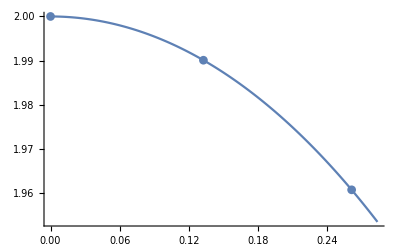

```mathematica
ModePlotOmega[2,0]
```

```mathematica
Options[ModeSolution]
```

{JacobianStep→-10,NoNegω→False,QNMPrecision→24,RadialCFDigits→8,RadialCFMinDepth→300,RadialDebug→0,RadialRelax→1,RCFPower→Null[],Rootϵ→Null[],SolutionDebug→0,SolutionIter→50,SolutionOscillate→10,SolutionSlow→10}

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

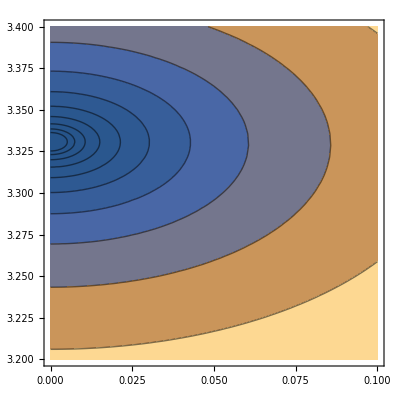

```mathematica
ContourPlot[Abs[PlotModeFunction[0,-2,0,8101001/16384000,4,ωr-ⅈ ωi,0,15]],{ωr,0,0.1},{ωi,3.2,3.4},Contours->{1/128,1/64,1/32,1/16,1/8,1/4,1/2,1,2,4,8}]
```

```mathematica
Plot3D[{Re[PlotModeFunctionL[0,-2,0,1579/3200,1,ωr-ⅈ ωi,0,15]],Im[PlotModeFunctionL[0,-2,0,1579/3200,1,ωr-ⅈ ωi,0,15]]},{ωr,-0.02,0.02},{ωi,3.15,3.23}]
```

-Graphics3D-

```mathematica
?PlotModeFunction
```

Arguments: n,s,m,a,Alm,ω,Nrcf,Nm
	 n -> Overtone level (integer).
	 s -> SpinWeight (integer).
	 m -> Azimuthal index (integer).
	 a -> Dimensionless spin parameter(rational or integer).
	 Alm -> Angular separation constant (integer).
	 Nrcf -> How deep into the continued fraction (integer).
	 Nm -> Number of azimuthal indecies(integer).

When in ContinuedFractionMode, package will require input for all the arguments and will use SelectMode
	 to replace ModeFunction with RadialCFRem.
When in PolynomialMode, n and Nrcf are not used in this plot function. Put dummy value in place.
PolynomialMode will use SelectMode to replace Modefunction with Starobinsky.

```mathematica
?ModeSolution
```

QNMSolution[n,s,l,m,a,ωg,Almg,ϵ,relax,Nrcf,Nm,ω0,Alm0,rl,rt] finds a solution of the coupled radial and angular Teukolsky equations with spin-weight s, 'magnetic' index m, and dimensionless angular momentum a.  ωg and Almg are initial guesses for the frequency and separation constant, which are assumed to be associated with azimuthal index l and overtone index n.

	The solution is found by iteration, calling AngularSpectralRoot and RadialLentzRoot until the magnitude of the change produced by either is less than 10^ϵ.  'relax' is an initial under-relaxation parameter used in updating the current guesses. For the radial equation, the continued fraction is truncated at the Nrcf^th term.  For the angular equation, Nm sets the size of the spectral approximation matrix.

	ω0, Alm0, rl, and rt are used to specify solution windows centered around the initial guesses ωg and Almg.  ω0 and Alm0 represent the prior solutions in a sequence of solutions.  |ω0-ωg| and |Alm0-Almg| set a length scale d for each solution.  The window for each solution is a portion of an anulus centered on the prior solution.  The difference between the inner and outer rings of the anulus is 2*rl*d with the guess solution centered between.  The width of the wedge is 2*rt*d along the outer ring.  Solutions falling outside the solution window for either quantity are rejected.  If rl=0 or rt=0, the solution is always accepted.

Options:
	 SolutionDebug→0 : Integer
		 Verbosity of debugging output for solutions iteration.  Increasing
		 value increases verbosity.
	 RadialDebug→0 : Integer
		 Verbosity of debugging output.  Increasing value increases verbosity.
	 RadialRelax→1: Rational(or Integer)
		 Under-relaxation parameter.
	 JacobianStep→-10
		 Log10 of relative step size used in numerical evaluation of the 
		 Jacobian in Newton's method.

```mathematica
?PlotModeFunction
```

Arguments: n,s,m,a,Alm,ω,Nrcf,Nm
	 n -> Overtone level (integer).
	 s -> SpinWeight (integer).
	 m -> Azimuthal index (integer).
	 a -> Dimensionless spin parameter(rational or integer).
	 Alm -> Angular separation constant (integer).
	 Nrcf -> How deep into the continued fraction (integer).
	 Nm -> Number of azimuthal indecies(integer).

When in ContinuedFractionMode, package will require input for all the arguments and will use SelectMode
	 to replace ModeFunction with RadialCFRem.
When in PolynomialMode, n and Nrcf are not used in this plot function. Put dummy value in place.
PolynomialMode will use SelectMode to replace Modefunction with Starobinsky.

```mathematica
SchwarzschildTTML[2,0,RadialDebug->4,SchDebug->1]
```

Computing (l=2,n=0)

RadialLentzStep :{KerrModes`Private`δωr→-9.99500374737656280568554×10^-6,KerrModes`Private`δωi→0.000999750149899958625930798} : {-0.576143985599936531025921-0.00576288000000000015423491 ⅈ,0}

δω=-9.99500374737656280568554×10^-6+0.000999750149899958625930798 ⅈ  root=0.576172806481592181039581

ω=4.99625262343801234499851×10^-9-2.00000024985009993123995 ⅈ

RadialLentzStep :{KerrModes`Private`δωr→-4.9962519992810206336147×10^-9,KerrModes`Private`δωi→2.49850084331214418590972×10^-7} : {-0.000143913666546010033345319-2.87784187061478967805879×10^-6 ⅈ,0}

δω=-4.9962519992810206336147×10^-9+2.49850084331214418590972×10^-7 ⅈ  root=0.000143942437774787012507994

Conv.Rate: 4000.80021491544868023167 : False

ω=6.24156991711383808045256×10^-16-2.00000000000001560002553 ⅈ

Set $MinPrecision =28

RadialLentzStep :{KerrModes`Private`δωr→-6.241569917113789396127541818×10^-16,KerrModes`Private`δωi→1.560002552656791373291584416×10^-14} : {-8.98561470330318828587217626×10^-12-3.595144272257598776511884402×10^-13 ⅈ,0}

δω=-6.241569917113789396127541818×10^-16+1.560002552656791373291584416×10^-14 ⅈ  root=8.992803913107519250534493049×10^-12

Conv.Rate: 1.600640036006678063732783896×10^7 : False

ω=4.868432501885096229986790674×10^-30-2. ⅈ

Set $MinPrecision =44

RadialLentzStep :{KerrModes`Private`δωr→-4.8684325018850962299867906736828033984999319×10^-30,KerrModes`Private`δωi→6.0742806119807339645384126163805259310871118×10^-29} : {-3.4987856325009027635741256671407633578783776×10^-26-2.8042171210858154284723914282116307745013191×10^-27 ⅈ,0}

δω=-4.8684325018850962299867906736828033984999319×10^-30+6.0742806119807339645384126163805259310871118×10^-29 ⅈ  root=3.5100053046707280435110922889030976789890763×10^-26

Conv.Rate: 2.5620485248671325973827021812564446137491955×10^14 : False

SetPrecision::precsm: Requested precision 24 is smaller than $MinPrecision. Using $MinPrecision instead.

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
$MinPrecision=24
```

24

```mathematica
SelectMode[PolynomialMode]
```

Mode set to find Polynomial solutions

```mathematica
Plot3D[Abs[PlotModeFunctionL[0,-2,1,50/100,1,ωr-ⅈ ωi,300,15]],{ωr,0,1},{ωi,1,2}]
```

-Graphics3D-

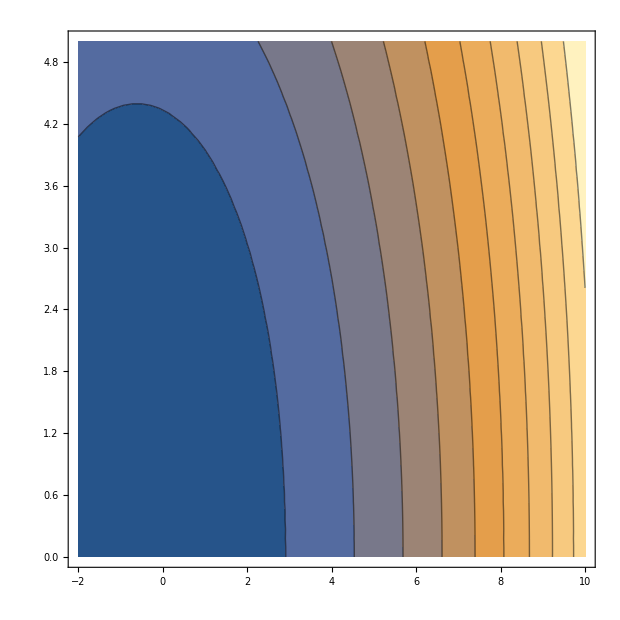

```mathematica
ContourPlot[Abs[PlotModeFunctionL[0,-2,-2,1/8,1,ωr-ⅈ ωi,3000,15]],{ωr,-2,10},{ωi,0,5},Contours->10]
```

```mathematica
Plot3D[{Re[PlotModeFunctionL[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]],Im[PlotModeFunctionL[0,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]]},{ωr,0,5},{ωi,0,5}]
```

-Graphics3D-

```mathematica
Plot3D[{Re[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]],Im[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]]},{ωr,0,4},{ωi,0,4}]
```

-Graphics3D-

```mathematica
RadialCFRem[0,-2,0,0,10,-ⅈ 10,2]
```

RadialCFRem[0,-2,0,0,10,-10 ⅈ,2]

```mathematica
SchwarzschildTTML[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

Have made it into RadialCFRem

Have made it into RadialCFRem

Have made it into RadialCFRem

«17 more identical outputs»

KerrModes`Private`RadialLentzStep::increase: Excessive increase in Precision, Abort

$Aborted

```mathematica
?SchwarzschildTTML
```

SchwarzschildTTML[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrTTML
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.